本Note的目的是计算随机变量函数的概率密度函数及其期望、方差

```mathematica
f[x_]:=PDF[NormalDistribution[μ,σ],x];(*自变量的概率密度函数*)
g[x_]:=1+A*x^B(*自变量与因变量之间的函数关系*)
D[g[x],x];(*A, B, x都是正实数，所以导数为正，存在反函数*)
h[y_]:=((y-1)/A)^(1/B);
D[h[y],y];(*A, B都是正实数，y>1，所以导数为正*)
```

```mathematica
w[y_]:=f[h[y]]*D[h[y],y]
w[y]
```

(ⅇ^(-((((-1+y)/A)^(1/B)-μ)^2)/(2 σ^2)) ((-1+y)/A)^(-1+1/B))/(A B √(2 π) σ)

计算期望与方差（这一部分运行不出来）

```mathematica
Integrate[(ⅇ^(-((((-1+y)/A)^(1/B)-μ)^2)/(2 σ^2)) ((-1+y)/A)^(-1+1/B))/(A B √(2 π) σ)*y,{y,1,∞},Assumptions->(Element[A,Reals]&&A>0&&Element[B,Reals]&&B>0&&Element[μ,Reals]&&μ>0&&Element[σ,Reals]&&σ>0)](*期望*)
```

实数样例

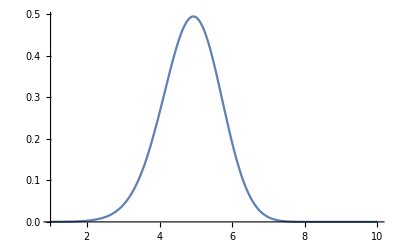

```mathematica
A=0.47;
B=0.780;
μ=15;
σ=4;
(*Plot[w[y],{y,1,10}]报错！*)
Plot[(ⅇ^(-((((-1+y)/A)^(1/B)-μ)^2)/(2 σ^2)) ((-1+y)/A)^(-1+1/B))/(A B √(2 π) σ),{y,1,10}](*这里是将w[y]复制过来的，直接使用w[y]会报错；我是刚开始使用Mathematica，错误经验不足，还请多多指教*)
```